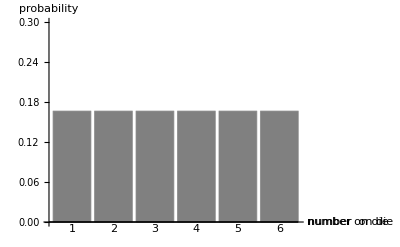

```mathematica
vX = Range[6];
vProbability = Table[1/6,{6}];
g1=Show[BarChart[vProbability,PlotRange->{Automatic,{0,0.3}},AxesLabel->{"number  on die ","probability "},ChartLabels->vX,BaseStyle->{FontSize->16},ChartStyle->{Gray}],ImagePadding->{{30,100},{30,30}}]
```

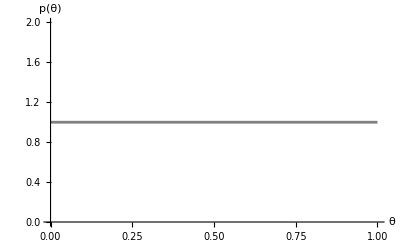

```mathematica
g2 = Show[Plot[PDF[UniformDistribution[{0,1}],θ],{θ,0,1},BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{θ,"p(θ)"}],ImagePadding->{{30,100},{30,30}}]
```

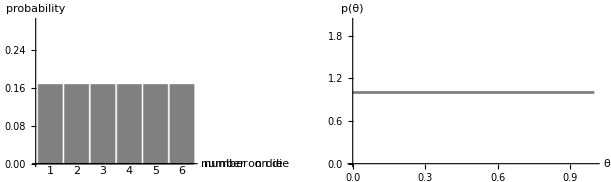

```mathematica
GraphicsRow[{g1,g2}]
```

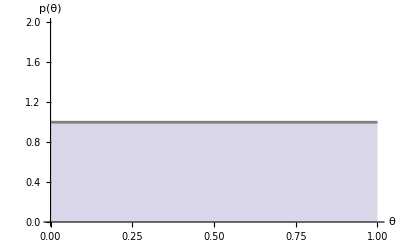

```mathematica
g2 = Show[Plot[PDF[UniformDistribution[{0,1}],θ],{θ,0,1},BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{θ,"p(θ)"},Filling->Axis],ImagePadding->{{30,100},{30,30}}]
```

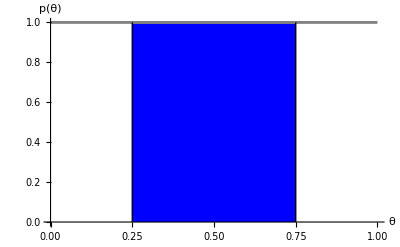

```mathematica
dist=PDF[UniformDistribution[{0,1}],#]&;
p1=Plot[dist@x,{x,0.25,0.75},Filling->Axis,FillingStyle->Blue,PlotRange->{{0,1},All},BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{θ,"p(θ)"}];
p2=Plot[dist@x,{x,0,1},Filling->None,PlotRange->{{0,1},All},BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{θ,"p(θ)"}];
Show[p1,p2,Epilog->{Black,Line[{{0.25,0},{0.25,1}}],Line[{{0.75,0},{0.75,1}}]}]
```